```mathematica
产生均匀分布
```

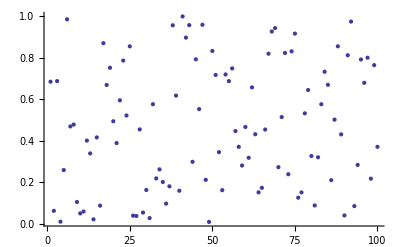

0.470751

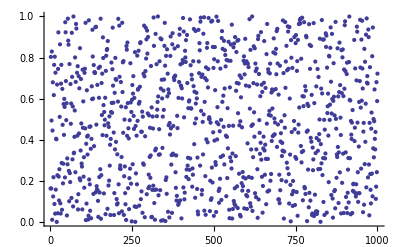

0.48632

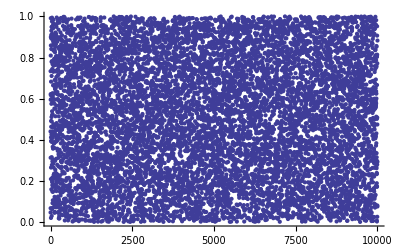

0.504347

```mathematica
Do[
T=Table[RandomReal[],{10^i}];
g=ListPlot[T,AxesStyle->Thickness[0.003]];
Print[g];Print[Mean[T]],{i,2,4}]
Clear[T]
```

```mathematica
产生高斯分布
```

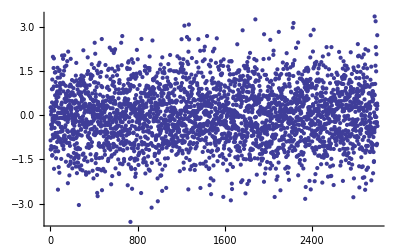

average = -6.25879×10^-9

```mathematica
dis=NormalDistribution[0,1];
T=Table[RandomReal[dis],{3000}];
ListPlot[T,AxesStyle->Thickness[0.003]]
Print["average = ",Mean[T] ]
Clear[T,dis]
```